```mathematica
Print["Your Working Folder"]
MyFolderX=NotebookDirectory[]

(* Store filepath (string) of PersonData_ALL_N_354842_ALL.txt file in FilePathX *)
FilePathX=StringJoin[MyFolderX,"shortterm.csv"]
(* Import Data > Store in the local variabe "Din" *)
Din=Import[FilePathX,"CSV",CharacterEncoding-> "UTF8","TextDelimiters"->"\""];
Print["How many lines does the file have?"]
NDataALL=Length[Din]
MatrixForm[Din]
```

Your Working Folder

/Users/test/Data & Code/

/Users/test/Data & Code/shortterm.csv

How many lines does the file have?

14

(data | Erongo | Hardap | Karas | Kavango | Khomas | Kuneenee | Ohangwena | Omaheke | Omusati | Oshana | Oshikoto | Otjozonjupa | Zambezi
Erongo | 0 | 207 | 232 | 200 | 1041 | 230 | 406 | 115 | 545 | 360 | 348 | 479 | 604
Hardap | 140 | 0 | 240 | 94 | 671 | 49 | 65 | 146 | 60 | 49 | 34 | 109 | 279
Karas | 114 | 209 | 0 | 215 | 394 | 22 | 122 | 123 | 112 | 155 | 68 | 115 | 518
Kavango | 81 | 43 | 57 | 0 | 297 | 56 | 60 | 91 | 42 | 96 | 101 | 259 | 434
Khomas | 1033 | 761 | 472 | 578 | 0 | 197 | 1163 | 674 | 1156 | 1066 | 862 | 991 | 1702
Kuneenee | 156 | 23 | 12 | 91 | 159 | 0 | 31 | 31 | 124 | 92 | 46 | 250 | 254
Ohangwena | 243 | 23 | 64 | 70 | 528 | 36 | 0 | 24 | 238 | 505 | 591 | 150 | 216
Omaheke | 94 | 88 | 31 | 154 | 582 | 43 | 73 | 0 | 82 | 80 | 57 | 214 | 183
Omusati | 213 | 32 | 87 | 21 | 578 | 118 | 273 | 25 | 0 | 616 | 257 | 163 | 365
Oshana | 202 | 34 | 98 | 60 | 631 | 87 | 722 | 40 | 796 | 0 | 681 | 178 | 406
Oshikoto | 205 | 31 | 65 | 87 | 472 | 50 | 619 | 20 | 224 | 643 | 0 | 315 | 231
Otjozonjupa | 400 | 98 | 81 | 454 | 890 | 252 | 237 | 187 | 260 | 252 | 337 | 0 | 305
Zambezi | 56 | 11 | 38 | 96 | 153 | 113 | 20 | 7 | 26 | 87 | 22 | 60 | 0)

```mathematica
DinN = Din[[2;;14,2;;14]]
```

{{0,207,232,200,1041,230,406,115,545,360,348,479,604},{140,0,240,94,671,49,65,146,60,49,34,109,279},{114,209,0,215,394,22,122,123,112,155,68,115,518},{81,43,57,0,297,56,60,91,42,96,101,259,434},{1033,761,472,578,0,197,1163,674,1156,1066,862,991,1702},{156,23,12,91,159,0,31,31,124,92,46,250,254},{243,23,64,70,528,36,0,24,238,505,591,150,216},{94,88,31,154,582,43,73,0,82,80,57,214,183},{213,32,87,21,578,118,273,25,0,616,257,163,365},{202,34,98,60,631,87,722,40,796,0,681,178,406},{205,31,65,87,472,50,619,20,224,643,0,315,231},{400,98,81,454,890,252,237,187,260,252,337,0,305},{56,11,38,96,153,113,20,7,26,87,22,60,0}}

```mathematica
nameType = Din[[1]][[2;;14]]
```

{Erongo,Hardap,Karas,Kavango,Khomas,Kuneenee,Ohangwena,Omaheke,Omusati,Oshana,Oshikoto,Otjozonjupa,Zambezi}

```mathematica
Head @DinN
```

List

```mathematica
DinT = Transpose[DinN]
```

{{0,140,114,81,1033,156,243,94,213,202,205,400,56},{207,0,209,43,761,23,23,88,32,34,31,98,11},{232,240,0,57,472,12,64,31,87,98,65,81,38},{200,94,215,0,578,91,70,154,21,60,87,454,96},{1041,671,394,297,0,159,528,582,578,631,472,890,153},{230,49,22,56,197,0,36,43,118,87,50,252,113},{406,65,122,60,1163,31,0,73,273,722,619,237,20},{115,146,123,91,674,31,24,0,25,40,20,187,7},{545,60,112,42,1156,124,238,82,0,796,224,260,26},{360,49,155,96,1066,92,505,80,616,0,643,252,87},{348,34,68,101,862,46,591,57,257,681,0,337,22},{479,109,115,259,991,250,150,214,163,178,315,0,60},{604,279,518,434,1702,254,216,183,365,406,231,305,0}}

{Erongo→Placed[Erongo,Center],Hardap→Placed[Hardap,Center],Karas→Placed[Karas,Center],Kavango→Placed[Kavango,Center],Khomas→Placed[Khomas,Center],Kuneenee→Placed[Kuneenee,Center],Ohangwena→Placed[Ohangwena,Center],Omaheke→Placed[Omaheke,Center],Omusati→Placed[Omusati,Center],Oshana→Placed[Oshana,Center],Oshikoto→Placed[Oshikoto,Center],Otjozonjupa→Placed[Otjozonjupa,Center],Zambezi→Placed[Zambezi,Center]}

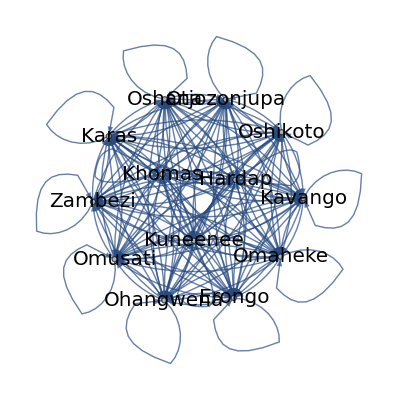

```mathematica
mat=Replace[DinT,0->Infinity,{2}];
NameFontSizeX=20;
NodeColorX=Black;
LabelsetBlack=Table[nameType[[i]]->Placed[ Style[nameType[[i]],FontFamily->"Helvetica",NameFontSizeX,NodeColorX],Center],{i,1,Length[nameType]}]
g=WeightedAdjacencyGraph[nameType,DinT,VertexLabels->LabelsetBlack]
```

```mathematica
N[GlobalClusteringCoefficient[g]]
```

1.

```mathematica
LClusteringCoeffX=N[LocalClusteringCoefficient[g]]
Mean[LClusteringCoeffX]
N[MeanClusteringCoefficient[g]]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

1.

1.

{}

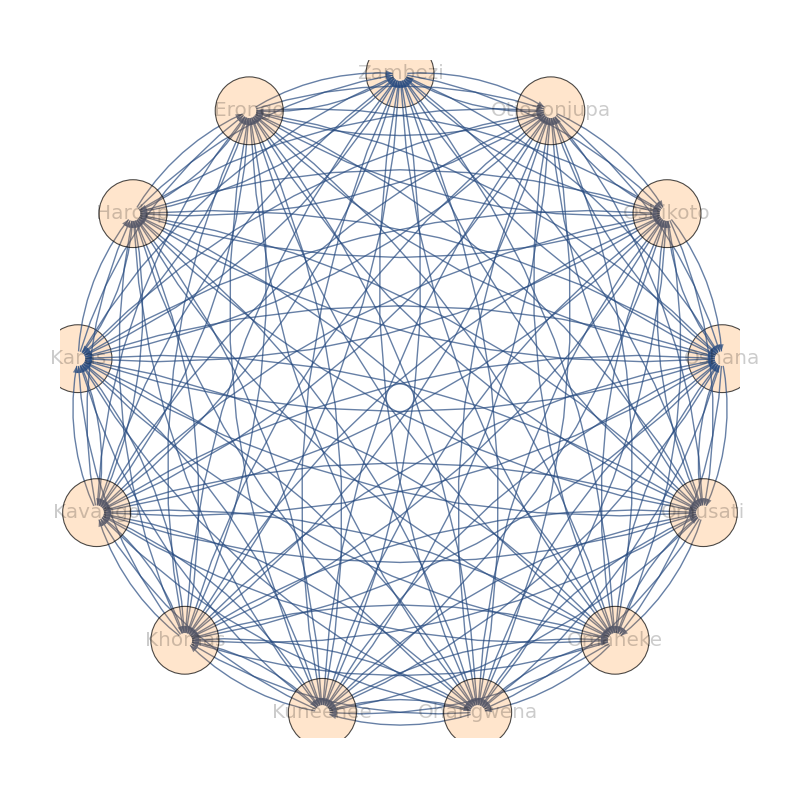

```mathematica
Circlesize=0.05;
r=Array[Circlesize&,Length[SPOnly]] (* Circle radius list *)

g=WeightedAdjacencyGraph[nameType,mat,VertexLabels->LabelsetBlack,VertexSize->Scaled[.10],VertexStyle->Directive[Orange,Opacity[.2]],GraphLayout->{"CircularEmbedding"} ,ImageSize->800]
```

```mathematica
gEdWe=AbsoluteOptions[g,EdgeWeight][[All,2]][[1]]  (* Get list of edge weights associated with each edge *)
Max[gEdWe]
```

{140,114,81,1033,156,243,94,213,202,205,400,56,207,209,43,761,23,23,88,32,34,31,98,11,232,240,57,472,12,64,31,87,98,65,81,38,200,94,215,578,91,70,154,21,60,87,454,96,1041,671,394,297,159,528,582,578,631,472,890,153,230,49,22,56,197,36,43,118,87,50,252,113,406,65,122,60,1163,31,73,273,722,619,237,20,115,146,123,91,674,31,24,25,40,20,187,7,545,60,112,42,1156,124,238,82,796,224,260,26,360,49,155,96,1066,92,505,80,616,643,252,87,348,34,68,101,862,46,591,57,257,681,337,22,479,109,115,259,991,250,150,214,163,178,315,60,604,279,518,434,1702,254,216,183,365,406,231,305}

1702

```mathematica
testL = Thread[Rule[EdgeList[g],gEdWe]]
```

{Erongo->Hardap→140,Erongo->Karas→114,Erongo->Kavango→81,Erongo->Khomas→1033,Erongo->Kuneenee→156,Erongo->Ohangwena→243,Erongo->Omaheke→94,Erongo->Omusati→213,Erongo->Oshana→202,Erongo->Oshikoto→205,Erongo->Otjozonjupa→400,Erongo->Zambezi→56,Hardap->Erongo→207,Hardap->Karas→209,Hardap->Kavango→43,Hardap->Khomas→761,Hardap->Kuneenee→23,Hardap->Ohangwena→23,Hardap->Omaheke→88,Hardap->Omusati→32,Hardap->Oshana→34,Hardap->Oshikoto→31,Hardap->Otjozonjupa→98,Hardap->Zambezi→11,Karas->Erongo→232,Karas->Hardap→240,Karas->Kavango→57,Karas->Khomas→472,Karas->Kuneenee→12,Karas->Ohangwena→64,Karas->Omaheke→31,Karas->Omusati→87,Karas->Oshana→98,Karas->Oshikoto→65,Karas->Otjozonjupa→81,Karas->Zambezi→38,Kavango->Erongo→200,Kavango->Hardap→94,Kavango->Karas→215,Kavango->Khomas→578,Kavango->Kuneenee→91,Kavango->Ohangwena→70,Kavango->Omaheke→154,Kavango->Omusati→21,Kavango->Oshana→60,Kavango->Oshikoto→87,Kavango->Otjozonjupa→454,Kavango->Zambezi→96,Khomas->Erongo→1041,Khomas->Hardap→671,Khomas->Karas→394,Khomas->Kavango→297,Khomas->Kuneenee→159,Khomas->Ohangwena→528,Khomas->Omaheke→582,Khomas->Omusati→578,Khomas->Oshana→631,Khomas->Oshikoto→472,Khomas->Otjozonjupa→890,Khomas->Zambezi→153,Kuneenee->Erongo→230,Kuneenee->Hardap→49,Kuneenee->Karas→22,Kuneenee->Kavango→56,Kuneenee->Khomas→197,Kuneenee->Ohangwena→36,Kuneenee->Omaheke→43,Kuneenee->Omusati→118,Kuneenee->Oshana→87,Kuneenee->Oshikoto→50,Kuneenee->Otjozonjupa→252,Kuneenee->Zambezi→113,Ohangwena->Erongo→406,Ohangwena->Hardap→65,Ohangwena->Karas→122,Ohangwena->Kavango→60,Ohangwena->Khomas→1163,Ohangwena->Kuneenee→31,Ohangwena->Omaheke→73,Ohangwena->Omusati→273,Ohangwena->Oshana→722,Ohangwena->Oshikoto→619,Ohangwena->Otjozonjupa→237,Ohangwena->Zambezi→20,Omaheke->Erongo→115,Omaheke->Hardap→146,Omaheke->Karas→123,Omaheke->Kavango→91,Omaheke->Khomas→674,Omaheke->Kuneenee→31,Omaheke->Ohangwena→24,Omaheke->Omusati→25,Omaheke->Oshana→40,Omaheke->Oshikoto→20,Omaheke->Otjozonjupa→187,Omaheke->Zambezi→7,Omusati->Erongo→545,Omusati->Hardap→60,Omusati->Karas→112,Omusati->Kavango→42,Omusati->Khomas→1156,Omusati->Kuneenee→124,Omusati->Ohangwena→238,Omusati->Omaheke→82,Omusati->Oshana→796,Omusati->Oshikoto→224,Omusati->Otjozonjupa→260,Omusati->Zambezi→26,Oshana->Erongo→360,Oshana->Hardap→49,Oshana->Karas→155,Oshana->Kavango→96,Oshana->Khomas→1066,Oshana->Kuneenee→92,Oshana->Ohangwena→505,Oshana->Omaheke→80,Oshana->Omusati→616,Oshana->Oshikoto→643,Oshana->Otjozonjupa→252,Oshana->Zambezi→87,Oshikoto->Erongo→348,Oshikoto->Hardap→34,Oshikoto->Karas→68,Oshikoto->Kavango→101,Oshikoto->Khomas→862,Oshikoto->Kuneenee→46,Oshikoto->Ohangwena→591,Oshikoto->Omaheke→57,Oshikoto->Omusati→257,Oshikoto->Oshana→681,Oshikoto->Otjozonjupa→337,Oshikoto->Zambezi→22,Otjozonjupa->Erongo→479,Otjozonjupa->Hardap→109,Otjozonjupa->Karas→115,Otjozonjupa->Kavango→259,Otjozonjupa->Khomas→991,Otjozonjupa->Kuneenee→250,Otjozonjupa->Ohangwena→150,Otjozonjupa->Omaheke→214,Otjozonjupa->Omusati→163,Otjozonjupa->Oshana→178,Otjozonjupa->Oshikoto→315,Otjozonjupa->Zambezi→60,Zambezi->Erongo→604,Zambezi->Hardap→279,Zambezi->Karas→518,Zambezi->Kavango→434,Zambezi->Khomas→1702,Zambezi->Kuneenee→254,Zambezi->Ohangwena→216,Zambezi->Omaheke→183,Zambezi->Omusati→365,Zambezi->Oshana→406,Zambezi->Oshikoto→231,Zambezi->Otjozonjupa→305}

```mathematica
gEdWe=Rescale[gEdWe,{0,Max[gEdWe]},{0,1}]
```

{70/851,57/851,81/1702,1033/1702,78/851,243/1702,47/851,213/1702,101/851,205/1702,200/851,28/851,9/74,209/1702,43/1702,761/1702,1/74,1/74,44/851,16/851,17/851,31/1702,49/851,11/1702,116/851,120/851,57/1702,236/851,6/851,32/851,31/1702,87/1702,49/851,65/1702,81/1702,19/851,100/851,47/851,215/1702,289/851,91/1702,35/851,77/851,21/1702,30/851,87/1702,227/851,48/851,1041/1702,671/1702,197/851,297/1702,159/1702,264/851,291/851,289/851,631/1702,236/851,445/851,153/1702,5/37,49/1702,11/851,28/851,197/1702,18/851,43/1702,59/851,87/1702,25/851,126/851,113/1702,203/851,65/1702,61/851,30/851,1163/1702,31/1702,73/1702,273/1702,361/851,619/1702,237/1702,10/851,5/74,73/851,123/1702,91/1702,337/851,31/1702,12/851,25/1702,20/851,10/851,187/1702,7/1702,545/1702,30/851,56/851,21/851,578/851,62/851,119/851,41/851,398/851,112/851,130/851,13/851,180/851,49/1702,155/1702,48/851,533/851,2/37,505/1702,40/851,308/851,643/1702,126/851,87/1702,174/851,17/851,34/851,101/1702,431/851,1/37,591/1702,57/1702,257/1702,681/1702,337/1702,11/851,479/1702,109/1702,5/74,7/46,991/1702,125/851,75/851,107/851,163/1702,89/851,315/1702,30/851,302/851,279/1702,7/23,217/851,1,127/851,108/851,183/1702,365/1702,203/851,231/1702,305/1702}

```mathematica
ThicknessBoost=2;
OpacityFactor=50; (* 1.15, 1, 1.1*)
RedGreenFactor=-1; (* 1 = Green, -1 = Red *)

(* Thread together the links with their modified color, opacity, and thickness values defined by gEdWe *)
(* The &/@gEdWe means that everywhere that there is a # in the Thread function it will use the corresponding list element in gEdWe *)
ModifiedEdgePropertiesX=
Thread[Rule[EdgeList[g],Directive[ColorData["RedGreenSplit"][Rescale[#,{-1*RedGreenFactor,1 *RedGreenFactor}]],Opacity[(OpacityFactor*#)],AbsoluteThickness[ThicknessBoost*#]]&/@gEdWe]];
Take[ModifiedEdgePropertiesX,3]
```

{Erongo->Hardap→Directive[RGBColor[1., 0.923008883666275, 0.923008883666275],Opacity[3500/851],AbsoluteThickness[140/851]],Erongo->Karas→Directive[RGBColor[1., 0.9373072338425382, 0.9373072338425382],Opacity[2850/851],AbsoluteThickness[114/851]],Erongo->Kavango→Directive[RGBColor[1., 0.9554551398354877, 0.9554551398354877],Opacity[2025/851],AbsoluteThickness[81/851]]}

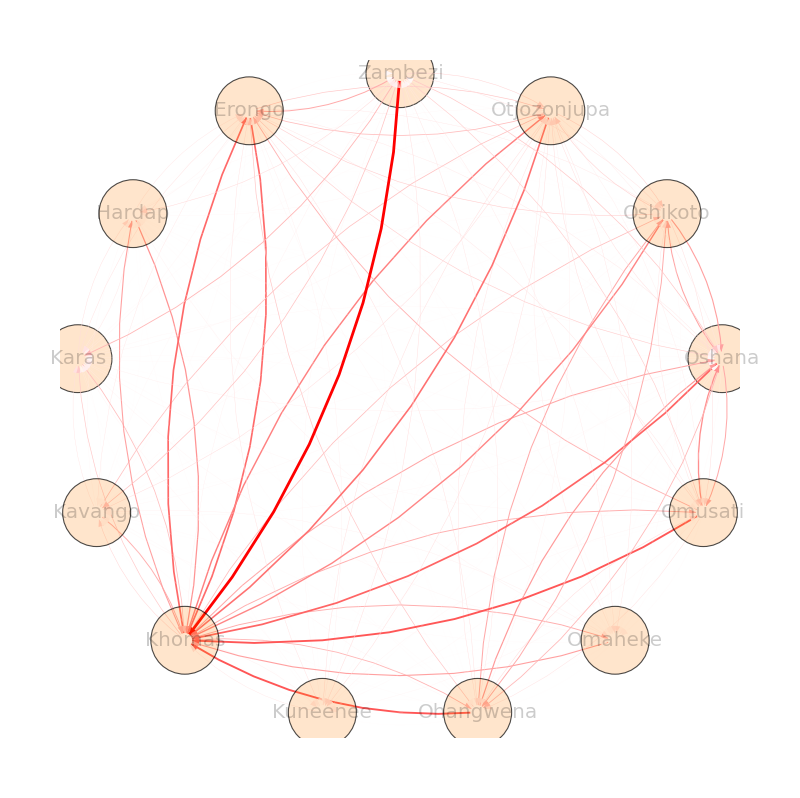

```mathematica
gra=SetProperty[g,EdgeStyle->ModifiedEdgePropertiesX];

Gfin=Show[gra,ImagePadding->{{100,100},{100,100}}]
```

```mathematica
DinS = Transpose[Din]
```

{{data,Erongo,Hardap,Karas,Kavango,Khomas,Kuneenee,Ohangwena,Omaheke,Omusati,Oshana,Oshikoto,Otjozonjupa,Zambezi},{Erongo,0,140,114,81,1033,156,243,94,213,202,205,400,56},{Hardap,207,0,209,43,761,23,23,88,32,34,31,98,11},{Karas,232,240,0,57,472,12,64,31,87,98,65,81,38},{Kavango,200,94,215,0,578,91,70,154,21,60,87,454,96},{Khomas,1041,671,394,297,0,159,528,582,578,631,472,890,153},{Kuneenee,230,49,22,56,197,0,36,43,118,87,50,252,113},{Ohangwena,406,65,122,60,1163,31,0,73,273,722,619,237,20},{Omaheke,115,146,123,91,674,31,24,0,25,40,20,187,7},{Omusati,545,60,112,42,1156,124,238,82,0,796,224,260,26},{Oshana,360,49,155,96,1066,92,505,80,616,0,643,252,87},{Oshikoto,348,34,68,101,862,46,591,57,257,681,0,337,22},{Otjozonjupa,479,109,115,259,991,250,150,214,163,178,315,0,60},{Zambezi,604,279,518,434,1702,254,216,183,365,406,231,305,0}}